```mathematica
returnFunc[n_]:=Module[
{aRand,aSum,A,b},
aRand=RandomReal[1,{n,n}];
aSum= (aRand+Transpose[aRand])/2;
A=aSum+3 IdentityMatrix[n];
b=RandomReal[10,n];
Function[vec,1/2+Transpose[vec].A.vec-b.vec]
]


n=2;
plotN=100;
 
f=returnFunc[n];

If[
n<=1||n>=7,
Print[],
If[n==2,
Plot3D[f[{x,y}],{x,-plotN,plotN},{y,-plotN,plotN}],
If[n==3,
ContourPlot3D[f[{x,y,z}],{x,-plotN,plotN},{y,-plotN,plotN},{z,-plotN,plotN} ],
Print[]
]
]
];
```

```mathematica
heavyBall[func_,x0_,alpha_,beta_,maxIter_,tol_]:=Module[
{x,xPrev,xNew,trajectory,iter,grad,errors,h=10^-5,n=Length[x0]},numericGrad[x_]:=Table[(func[x+h*UnitVector[n,i]]-func[x-h*UnitVector[n,i]])/(2h),{i,n}];

xPrev=x0;
grad=numericGrad[x0];
x=x0-alpha*grad;
trajectory={xPrev,x};
errors={Norm[grad]};

For[iter=1,iter<=maxIter,iter++,
grad=numericGrad[x];
xNew=x-alpha*grad+beta*(x-xPrev);
AppendTo[errors,Norm[grad]];
AppendTo[trajectory,xNew];

If[Norm[xNew-x]<tol,
Print["Достигнута точность! Iter: ", iter];
Break[]
];
xPrev=x;
x=xNew;
];
{x,trajectory,errors}
];

x0=RandomReal[1000,n];
alpha=0.1;
beta=0.8;
maxIter=1000;
tol=10^-6;
```

Достигнута точность! Iter: 174

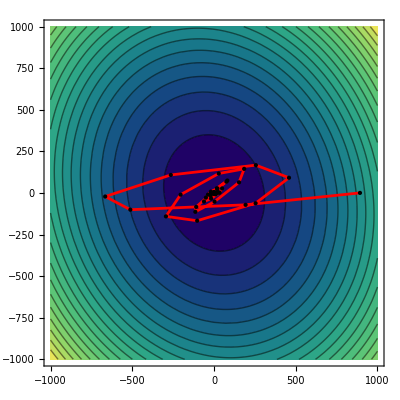

```mathematica
result=heavyBall[f,x0,alpha,beta,maxIter,tol];

xMin = result[[1]];
trajectory=result[[2]];

plot=ListPlot[
trajectory,
PlotStyle->Directive[Red,PointSize[Small]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];


Show[ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"BlueGreenYellow"],plot]

animation=ListAnimate[
Table[
Show[
ContourPlot[
f[{x,y}],{x,-300,300},{y,-300,300}, Contours->20
],
Graphics[
{Black,PointSize[Large],
Point[trajectory[[i]]],Red,Line[trajectory[[1;;i]]],
Text["Шаг: "<>ToString[i],Scaled[{0.1,0.9}]
]
}
]
],
{i,0,Length[trajectory],5}
]
]

Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/animation.gif",animation,"GIF","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
```

```mathematica
|
```